# Spectral Lags in Very High Energy Emission of GRBs

## Configuration

```mathematica
SetDirectory["~/Projects/GammaRays/"];
```

## Numerical functions

### findRoot

Only works for monotonously increasing functions, which have a root for var > 0

```mathematica
findRoot[func_,{var_,start_?NumericQ}]:=Block[{left,right},
If[(func/.var->start)<0,
left=start;
right=2.start;
While[(func/.var->right)<0,right*=2;left*=2];
,
right=start;
left=.5start;
While[(func/.var->left)>0,left*=.5;right*=.5];
];
FindRoot[func,{var,left,right}]
]
```

## Model

### Parameters

```mathematica
universe={Hobs_,Ωm_};
```

```mathematica
Options[defaultUniverse]={Hobs->2.*^-18,Ωm->0.317};
defaultUniverse[OptionsPattern[]]:={OptionValue[Hobs],OptionValue[Ωm]};
```

```mathematica
population={density0_,index_,zc_};
```

```mathematica
Options[defaultPopulation]={density0->0.655427*^-50,index->3,zc->3.};
defaultPopulation[OptionsPattern[]]:={OptionValue[density0],OptionValue[index],OptionValue[zc]};
```

```mathematica
burst={γ_,η0_,r0_,n_,ω0_,θ0_,k_,α_};
```

```mathematica
Options[defaultBurst]={γ->300,η0->8.14796255480381*^34,r0->3.357930930824906*^6,n->22.5269,ω0->1.,θ0->0.0000502035,k->-0.699813,α->-0.626944};
defaultBurst[OptionsPattern[]]:={OptionValue[γ],OptionValue[η0],OptionValue[r0],OptionValue[n],OptionValue[ω0],OptionValue[θ0],OptionValue[k],OptionValue[α]};
```

```mathematica
defaultDetectorArea[]:=5.563*^-18;
```

```mathematica
observer={detectorArea_,z_,χ_};
```

```mathematica
Options[defaultObserver]={detectorArea->defaultDetectorArea[],z->2.1062,χ->0.00541037};
defaultObserver[OptionsPattern[]]={OptionValue[detectorArea],OptionValue[z],OptionValue[χ]};
```

### Relativity

```mathematica
v[γ_]:=√(1-1/γ^2);
```

### Cosmology

```mathematica
ΩΛ[Ωm_]:=1-Ωm;
```

```mathematica
distance[universe,z_]:=1/Hobs √(1/ΩΛ[Ωm])((1+z)Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm](1+z)^3]-Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm]]);
```

```mathematica
photonSphereArea[universe_,z_]:=4π distance[universe,z]^2;
```

```mathematica
burstsSphereArea[universe_,z_]:=(4π distance[universe,z]^2)/(1+z)^2;
```

```mathematica
shellVolumePerRedshift[universe,z_]:=(4π distance[{Hobs,Ωm},z]^2)/(1+z)^3 1/(Hobs √(Ωm(1+z)^3+ΩΛ[Ωm]));
```

### Light curve

```mathematica
i[burst,z_,χ_,ω_,θ_,ϕ_]:=
If[ω==∞,
0,
1/(2k)ω(ω/ω0)^α ExpIntegralE[(α+1)/(2k)+1,(θ/θ0)^2(ω/ω0)^(-2k)(v[γ]γ(1+z)(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ]))^(-2k)]
];
```

```mathematica
j[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z))^3 π/(n Sin[(3π)/n]),
τ^3/3 Hypergeometric2F1[1,3/n,(n+3)/n,-(τ/(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z)))^n]
];
```

```mathematica
p[universe_,burst,observer,{θ_,ϕ_},{τ1_,τ2_},{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
Re[detectorArea/photonSphereArea[universe,z] η0/(v[γ]γ(1+z))^(2-α)1/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ])]
];
```

```mathematica
p[universe_,burst,{detectorArea_,z_,χ_?NumericQ},{τ1_,τ2_},{ω1_,ω2_}]:=p[{Hobs,Ωm},{γ,η0,r0,n,ω0,θ0,k,α},{detectorArea,z,χ},{τ1,τ2},{ω1,ω2}]=Block[{burstValues,θPoints,result},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
θPoints={θ,0}~Join~Sort[Select[{θ0/10.,θ0,10.θ0,100.θ0,1./γ,10./γ,100./γ,χ-1./γ,χ-10./γ,χ-100./γ,χ+1./γ,χ+10./γ,χ+100./γ},#>0&]]~Join~{∞};
result=NIntegrate[2θ p[universe,burstValues,{detectorArea,z,χ},{θ,ϕ},{τ1,τ2},{ω1,ω2}],Evaluate@θPoints,{ϕ,0,π},MinRecursion->3];
If[result>0,result,Abort[]]
]
```

### Light curve time derivative

```mathematica
jτ[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
0,
Re[τ^2/(1+((2τ)/(r0 (1+z) (-2+2/v[γ]+θ^2+χ^2-2 θ χ Cos[ϕ])))^n)]
];
```

```mathematica
pτ[universe_,burst,observer,{θ_,ϕ_},τ_,{ω1_,ω2_}]:=Block[{burstValues},
Re[detectorArea/photonSphereArea[universe,z] η0/(v[γ]γ(1+z))^(2-α)1/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ]]
]
```

```mathematica
pτ[universe_,burst,{detectorArea_,z_,χ_?NumericQ},τ_,{ω1_,ω2_}]:=Block[{burstValues,θPoints,result},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
θPoints={θ,0}~Join~Sort[Select[{θ0/10.,θ0,10.θ0,100.θ0,1./γ,10./γ,100./γ,χ-1./γ,χ-10./γ,χ-100./γ,χ+1./γ,χ+10./γ,χ+100./γ},#>0&]]~Join~{∞};
result=NIntegrate[2θ pτ[universe,burstValues,{detectorArea,z,χ},{θ,ϕ},τ,{ω1,ω2}],Evaluate@θPoints,{ϕ,0,π},MinRecursion->3];
If[result>0,result,Abort[]]
]
```

### Duration

```mathematica
Options[duration]={part->0.99};
duration[universe_,burst,observer,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,observerValues,p∞,precision,pi},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
observerValues={detectorArea,z,χ};
p∞=p[universe,burstValues,observerValues,{0.,∞},{ω1,ω2}];
pi[τ_?NumericQ]:=p[universe,burstValues,observerValues,{0.,τ},{ω1,ω2}];
τ/.findRoot[pi[τ]-OptionValue[part]p∞,{τ,r0/γ^2(1.+z)}]
];
```

### Stretching factor

```mathematica
Options[κ]={pointCount->20,accurateQ->True};
κ[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{p12∞,p23∞,diff,diffτ,τmiddle,τend,diffDifference,n,accQ},
p12∞=p[universe,burst,observer,{0.,∞},{ω1,ω2}];
p23∞=p[universe,burst,observer,{0.,∞},{ω2,ω3}];
diff[τ_?NumericQ,κ_?NumericQ]:=p[universe,burst,observer,{0.,τ},{ω1,ω2}]/(p12∞)-p[universe,burst,observer,{0.,κ τ},{ω2,ω3}]/(p23∞);
diffτ[τ_?NumericQ,κ_?NumericQ]:=pτ[universe,burst,observer,τ,{ω1,ω2}]/(p12∞)-κ pτ[universe,burst,observer,κ τ,{ω2,ω3}]/(p23∞);
accQ=OptionValue[accurateQ];
n=OptionValue[pointCount];
If[TrueQ[accQ],
τend=duration[universe,burst,observer,{ω1,ω3}];
diffDifference[κ_?NumericQ]:=Block[{it,diffτValues,maxDifference,minDifference,currentDifference},
diffτValues=Table[{τ,diffτ[τ,κ]},{τ,τend/n,τend,τend/n}];
maxDifference=0.;
minDifference=0.;
For[it=1,it<Length[diffτValues],it++,
If[Sign[diffτValues⟦it,2⟧]≠Sign[diffτValues⟦it+1,2⟧],
currentDifference=diff[τ/.FindRoot[diffτ[τ,κ],{τ,diffτValues⟦it,1⟧,diffτValues⟦it+1,1⟧}],κ];
maxDifference=Max[maxDifference,currentDifference];
minDifference=Min[minDifference,currentDifference];
];
];
maxDifference+minDifference
];
κi/.findRoot[-diffDifference[κi],{κi,1.}]
,
τmiddle=duration[universe,burst,observer,{ω1,ω3},part->0.5];
κi/.findRoot[-diff[τmiddle,κi],{κi,1.}]
]
];
```

```mathematica
SetSharedFunction[κStoredValues];
Options[κCache]={pointCount->20,accurateQ->True};
κCache[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{},
If[Not[NumberQ[κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[pointCount],OptionValue[accurateQ]]]],κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[pointCount],OptionValue[accurateQ]]=κ[universe,burst,observer,{ω1,ω2,ω3},pointCount->OptionValue[pointCount],accurateQ->OptionValue[accurateQ]]];
κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[pointCount],OptionValue[accurateQ]]
];
```

```mathematica
κSave[]:=DumpSave["kappa.mx",κStoredValues];
```

```mathematica
κLoad[]:=If[FileExistsQ["kappa.mx"],<<"kappa.mx"];
```

### Total Energy

```mathematica
energy[burst,ω1_]:=(16 π^3)/(3n(-2k-α-2)Sin[(3π)/n])γ^(-2k-α)(1-1/(4 γ^2))η0 r0^3 θ0^2 ω0^(-2k-α)/ω1^(-2k-α-2);
```

### Distribution of stretching factors

```mathematica
Options[zmax]={minParticles->10};
zmax[universe_,burst_,detectorArea_,χ_,{ω1_,ω2_},OptionsPattern[]]:=Block[{int,z1,z2},
int[z_?NumericQ]:=p[universe,burst,{detectorArea,z,χ},{0,∞},{ω1,ω2}]-OptionValue[minParticles];
z1=1;
While[int[z1]<0,z1/=2.];
z2=1;
While[int[z2]>0,z2*=2.];
z/.FindRoot[int[z],{z,z1,z2}]
];
```

```mathematica
Options[χmax]={minParticles->10};
χmax[universe_,burst,detectorArea_,z_,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,int,χ0},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
int[χ_?NumberQ]:=p[universe,burstValues,{detectorArea,z,χ},{0.,∞},{ω1,ω2}]-OptionValue[minParticles];
If[int[0]<0,
Return[0],
χ0=1/γ;
While[int[χ0]>0,χ0*=2.;];
];
χ/.FindRoot[int[χ],{χ,0,χ0}]
];
```

```mathematica
burstDensity[population,z_]:=density0(1+z)^index Exp[-z/zc];
```

```mathematica
phaseVolume[universe_,population_,{z1_?NumberQ,z2_?NumberQ}]:=NIntegrate[shellVolumePerRedshift[universe,z]burstDensity[population,z],{z,z1,z2}];
```

```mathematica
randomRedshift[universe_,population_,{z1_,z2_}]:=Block[{total,chosenVolume},
total=phaseVolume[universe,population,{z1,z2}];
chosenVolume=RandomReal[total];
z/.FindRoot[phaseVolume[universe,population,{z1,z}]-chosenVolume,{z,z1,z2}]
];
```

```mathematica
randomAngle[{χ1_,χ2_}]:=√RandomReal[{χ1^2,χ2^2}];
```

```mathematica
inRegionQ[region_,point_]:=Block[{i},
For[i=1,i≤Length[region],i++,
If[region[[i]][[1]]≤point[[1]]&&region[[i]][[2]]≤point[[2]],Return[True]];
];
Return[False];
];
```

```mathematica
addToRegion[region_,point_]:=Block[{i,j},
For[i=1,i≤Length[region],i++,
If[region[[i]][[1]]>point[[1]],
If[i==1||region[[i-1]][[2]]>point[[2]],
For[j=i,j≤Length[region]&&region[[j]][[2]]>point[[2]],j++];
Return[Insert[Drop[region,{i,j-1}],point,i]];
,
Return[region];
];
];
];
If[Length[region]==0||region[[Length[region]]][[2]]>point[[2]],
Return[Insert[region,point,Length[region]+1]];
,
Return[region];
];
];
```

```mathematica
Options[plotRegion]={axesOrigin->Automatic};
plotRegion[region_,range_,OptionsPattern[]]:=Block[{plotPoints},
If[Length[region]==0,Return[ListPlot[{Missing},PlotRange->range]]];
plotPoints=Flatten[Table[{region[[i]],{region[[i+1]][[1]],region[[i]][[2]]}},{i,1,Length[region]-1}],1];
AppendTo[plotPoints,region[[Length[region]]]];
AppendTo[plotPoints,{range[[1]][[2]],region[[Length[region]]][[2]]}];
ListPlot[plotPoints,PlotStyle->LightRed,Joined->True,PlotRange->range,Filling->Top,FillingStyle->LightRed,AxesOrigin->OptionValue[axesOrigin]]
];
```

```mathematica
burstSample::usage="burstSample computes a sample of properties of uniformly distributed GRBs. Possible values for computedValues are {z, χ, pTotal, pLow, pHigh, duration, κ}";
Options[burstSample]={randomSeed->"Gamma Rays",zmin->0.1,computedValues->{"z","χ","pLow","pHigh","duration","κ"},minParticles->10,monitorQ->False,logQ->False,accurateQ->True,pointCount->20};
burstSample[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},n_,OptionsPattern[]]:=Block[{
z2,χ2,it,zc,χc,pointsChosen,startedCount,completedCount,result,pointResult,region,print
},
If[OptionValue[logQ],Print["initializing"]];
SeedRandom[OptionValue[randomSeed]];
pointsChosen={};
startedCount=0;
completedCount=0;
SetSharedVariable[completedCount];
SetSharedVariable[startedCount];
region={};
it=0;
If[OptionValue[monitorQ],
print=PrintTemporary[Dynamic[
If[it==0,"initializing",
If[startedCount>0,ToString[completedCount]<>"/"<>ToString[n]<>" bursts computed",
ToString[Length[pointsChosen]]<>"/"<>ToString[n]<>" bursts chosen"
]
]
]]];
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3},minParticles->OptionValue[minParticles]];
χ2=χmax[universe,burst,detectorArea,OptionValue[zmin],{ω2,ω3},minParticles->OptionValue[minParticles]];
For[it=1,it≤n,it++,
zc=randomRedshift[universe,population,{OptionValue[zmin],z2}];
χc=randomAngle[{0,χ2}];
If[inRegionQ[region,{zc,χc}],it--,
If[p[universe,burst,{detectorArea,zc,χc},{0,∞},{ω2,ω3}]≥10.,
AppendTo[pointsChosen,{zc,χc}];
If[OptionValue[logQ],Print[ToString[Length[pointsChosen]]<>"/"<>ToString[n]<>" values chosen"]];
,
region=addToRegion[region,{zc,χc}];
it--;
];
];
];
κLoad[];
result=ParallelTable[
startedCount++;
pointResult=ReleaseHold[OptionValue[computedValues]/.{
"z"->Hold[point[[1]]],
"χ"->Hold[point[[2]]],
"pTotal"->Hold[p[universe,burst,Flatten[{detectorArea,point}],{0,∞},{ω1,ω3}]],
"pLow"->Hold[p[universe,burst,Flatten[{detectorArea,point}],{0,∞},{ω1,ω2}]],
"pHigh"->Hold[p[universe,burst,Flatten[{detectorArea,point}],{0,∞},{ω2,ω3}]],
"duration"->Hold[duration[universe,burst,Flatten[{detectorArea,point}],{ω1,ω3}]],
"κ"->Hold[κCache[universe,burst,Flatten[{detectorArea,point}],{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ],pointCount->OptionValue[pointCount]]]
}];
completedCount++;
If[OptionValue[logQ],Print[ToString[completedCount]<>"/"<>ToString[n]<>" bursts computed"]];
pointResult,{point,pointsChosen},Method->"FinestGrained"];
κSave[];
If[OptionValue[monitorQ],
NotebookDelete[print];
];
UnsetShared[completedCount];
UnsetShared[startedCount];
result
];
```

### Very high energy bursts fraction

```mathematica
Options[burstFraction]={minParticles->10};
burstFraction[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{z1,z2,int},
z1=zmax[universe,burst,detectorArea,0,{ω1,ω3},minParticles->OptionValue[minParticles]];
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3},minParticles->OptionValue[minParticles]];
int[z_?NumberQ,{ωl_,ωr_}]:=burstDensity[population,z]shellVolumePerRedshift[universe,z] χmax[universe,burst,detectorArea,z,{ωl,ωr}]^2;
NIntegrate[int[z,{ω2,ω3}],{z,0,z2}]/NIntegrate[int[z,{ω1,ω3}],{z,0,z1}]
];
```

### Parameter fit

#### GRB 090926A

```mathematica
κLogTarget090926A=Mean[{Log[1.99],Log[6.62]}]
```

1.28912

```mathematica
κLogError090926A=(Log[6.62]-Log[1.99])/2
```

0.60098

```mathematica
photonRatioLogTarget090926A=Log[0.0606777]
```

-2.80218

```mathematica
totalPhotonCount090926A=179.989;
```

```mathematica
duration090926A=219.5;
```

#### GRB 090902B

```mathematica
κLogTarget090902B=Mean[{Log[0.36],Log[0.89]}]
```

-0.569093

```mathematica
κLogError090902B=(Log[0.89]-Log[0.36])/2
```

0.452559

#### Combined test

```mathematica
durationNormalize[universe_,burst,observer_,targetDuration_,{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
burstValues[[3]]=targetDuration r0/duration[universe,burstValues,observer,{ω1,ω2}];
burstValues
]
```

```mathematica
energyNormalize[universe_,burst,observer_,photonCount_,{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
burstValues[[2]]=photonCount η0/p[universe,burstValues,observer,{0,∞},{ω1,ω2}];
burstValues
]
```

```mathematica
normalizedBurst[universe_,burst_,observer_,targetDuration_,photonCount_,{ω1_,ω2_}]:=energyNormalize[universe,durationNormalize[universe,burst,observer,targetDuration,{ω1,ω2}],observer,photonCount,{ω1,ω2}]
```

```mathematica
Options[fitTestSingleBurst]={sampleSize->10,penalizationFactor->400,maxEnergy->6*^53,accurateQ->True,logQ->False,testWeights->{1,1,1,1}};
fitTestSingleBurst[universe_,population_,burst,observer,{ω1_,ω2_,ω3_},totalPhotonCount_,{κLogTarget_,κLogError_},{κMinLogTarget_,κMinLogError_},{photonRatioLogTarget_,photonRatioLogError_},{photonRatioMedianLogTarget_,photonRatioMedianLogError_},OptionsPattern[]]:=Block[{result,sample,pLow,pHigh,κ0,κTest,κMinTest,photonRatioTest,photonRatioMedianTest,burstValues},
If[OptionValue[logQ],Print[Row[{"trying ",{{γ,η0,r0,n,ω0,θ0,k,α},{z,χ}}}]]];
result=If[k+α/2+1≥0,OptionValue[penalizationFactor],
burstValues=energyNormalize[universe,{γ,η0,r0,n,ω0,θ0,k,α},{detectorArea,z,χ},totalPhotonCount,{ω1,ω3}];
If[energy[burstValues,ω1]>OptionValue[maxEnergy],OptionValue[penalizationFactor],
sample=burstSample[universe,population,burstValues,detectorArea,{ω1,ω2,ω3},OptionValue[sampleSize],computedValues->{"pTotal","κ"},accurateQ->OptionValue[accurateQ]];
pLow=p[universe,burstValues,{detectorArea,z,χ},{0,∞},{ω1,ω2}];
pHigh=p[universe,burstValues,{detectorArea,z,χ},{0,∞},{ω2,ω3}];
κ0=κCache[universe,burstValues,{detectorArea,z,χ},{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ]];
κTest=(Log[κ0]-κLogTarget)/κLogError;
κMinTest=Max[0,(Log@Min@sample[[All,2]]-κMinLogTarget)/κMinLogError];

photonRatioTest=(Log[pHigh/pLow]-photonRatioLogTarget)/photonRatioLogError;
photonRatioMedianTest=(Log[(pLow+pHigh)/(Median@sample[[All,1]])]-photonRatioMedianLogTarget)/photonRatioMedianLogError;
Total[OptionValue[testWeights]{κTest^2,κMinTest^2,photonRatioTest^2,photonRatioMedianTest^2}]
]
];
If[OptionValue[logQ],Print[{result,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},burstValues,{z,χ}}]];
result
]
```

```mathematica
Options[findSingleBurstFit]={accurateQ->True,logQ->False,sampleSize->10,penalizationFactor->400,maxEnergy->6*^53,η0->8.4*^37,r0->1.2*^6,χMaxFactor->30.,detectorArea->5.563*^-18,nMin->3.5,testWeights->{1,1,1,1}};
findSingleBurstFit[universe_,population_,{γ_,ω0_},z_,{ω1_,ω2_,ω3_},totalPhotonCount_,{κLogTarget_,κLogError_},{κMinLogTarget_,κMinLogError_},{photonRatioLogTarget_,photonRatioLogError_},{photonRatioMedianLogTarget_,photonRatioMedianLogError_},initialPoints_,OptionsPattern[]]:=Block[{testFunction,η0,r0,detectorArea,sSize,penFactor,mEnergy,accQ,lQ,weights},
η0=OptionValue[η0];
r0=OptionValue[r0];
detectorArea=OptionValue[detectorArea];
sSize=OptionValue[sampleSize];
penFactor=OptionValue[penalizationFactor];
mEnergy=OptionValue[maxEnergy];
accQ=OptionValue[accurateQ];
lQ=OptionValue[logQ];
weights=OptionValue[testWeights];
testFunction[nj_?NumericQ,θ0j_?NumericQ,kj_?NumericQ,αj_?NumericQ,χj_?NumericQ]:=fitTestSingleBurst[universe,population,{γ,η0,r0,nj,ω0,Exp[θ0j],kj,αj},{detectorArea,z,Exp[χj]},{ω1,ω2,ω3},totalPhotonCount,{κLogTarget,κLogError},{κMinLogTarget,κMinLogError},{photonRatioLogTarget,photonRatioLogError},{photonRatioMedianLogTarget,photonRatioMedianLogError},sampleSize->sSize,penalizationFactor->penFactor,maxEnergy->mEnergy,accurateQ->accQ,logQ->lQ,testWeights->weights];
NMinimize[{testFunction[nj,θ0j,kj,αj,χj],nj>OptionValue[nMin],kj<0,χj≤Log[OptionValue[χMaxFactor]/γ]},{nj,θ0j,kj,αj,χj},Method->{"NelderMead","InitialPoints"->initialPoints}]
]
```

### Visualization

#### Model scheme

```mathematica
Options[modelScheme]={centralEngineSize->0.03,jetRadius->0.3,lowAngle->0.1,highAngle->0.01,observerSize->0.03,observerDistance->1,observerAngle->0.09,centralEngineQ->True,centralEngineLabelQ->False,jetQ->True,jetLabelQ->False,epQ->True,γQ->True,observerQ->True,observerLabelQ->False,FontSize->10,ImageSize->Automatic};
modelScheme[OptionsPattern[]]:=Block[{i,ti,redX,redY,blueX,blueY,observerX,observerY},
Graphics[{
{If[OptionValue[centralEngineQ],Black,Transparent],Disk[{0,0},OptionValue[centralEngineSize]]},
{If[OptionValue[centralEngineLabelQ],Black,Transparent],Text[Style["Central\nEngine",FontSize->OptionValue[FontSize]],{0,-OptionValue[centralEngineSize]},Top]},

observerX=OptionValue[observerDistance]Cos[OptionValue[observerAngle]];
observerY=OptionValue[observerDistance]Sin[OptionValue[observerAngle]];
{If[OptionValue[observerQ],Darker[Green],Transparent],Disk[{observerX,observerY},OptionValue[observerSize]]},
{If[OptionValue[observerLabelQ],Darker[Green],Transparent],
Text[Style["Observer",FontSize->OptionValue[FontSize]],{observerX,observerY+OptionValue[centralEngineSize]},Bottom]},

{If[OptionValue[jetQ],Opacity[0.1],Opacity[0]],Red,Disk[{0,0},OptionValue[jetRadius],{-OptionValue[lowAngle],OptionValue[lowAngle]}]},
{Thick,Red,If[OptionValue[jetQ],Opacity[1],Opacity[0]],Circle[{0,0},OptionValue[jetRadius],{-OptionValue[lowAngle],OptionValue[lowAngle]}]},
{If[OptionValue[jetQ],Opacity[0.1],Opacity[0]],Blue,Disk[{0,0},OptionValue[jetRadius],{-OptionValue[highAngle],OptionValue[highAngle]}]},
{Thick,Blue,If[OptionValue[jetQ],Opacity[1],Opacity[0]],Circle[{0,0},OptionValue[jetRadius],{-OptionValue[highAngle],OptionValue[highAngle]}]},
{Red,If[OptionValue[jetLabelQ],Opacity[1],Opacity[0]],Text[Style["Shock\nFront",FontSize->OptionValue[FontSize]],{1.03OptionValue[jetRadius]Cos[OptionValue[lowAngle]/2],-OptionValue[jetRadius]Sin[OptionValue[lowAngle]/2]},{Left,Top}]},

redX=OptionValue[jetRadius] Cos[Min[OptionValue[lowAngle],OptionValue[observerAngle]]];
redY=OptionValue[jetRadius] Sin[Min[OptionValue[lowAngle],OptionValue[observerAngle]]];
blueX=OptionValue[jetRadius] Cos[Min[OptionValue[highAngle],OptionValue[observerAngle]]];
blueY=OptionValue[jetRadius] Sin[Min[OptionValue[highAngle],OptionValue[observerAngle]]];
{Red,If[OptionValue[epQ],Opacity[1],Opacity[0]],Line[{{0,0},{redX,redY}}]},
{Red,If[OptionValue[epQ],Opacity[1],Opacity[0]],Text[Style["e^±, p^±",FontSize->OptionValue[FontSize]],{redX/2,redY/2},{Right,Bottom}]},
{Blue,If[OptionValue[epQ],Opacity[1],Opacity[0]],Line[{{0,0},{blueX,blueY}}]},
{Blue,If[OptionValue[epQ],Opacity[1],Opacity[0]],Text[Style["e^±, p^±",FontSize->OptionValue[FontSize]],{blueX/2,blueY/2},{Left,Top}]},

{Dashed,If[OptionValue[γQ],Opacity[1],Opacity[0]],Red,Line[{{redX,redY},{observerX,observerY}}]},
{Red,If[OptionValue[γQ],Opacity[1],Opacity[0]],Text[Style["γ",FontSize->OptionValue[FontSize]],{(redX+observerX)/2,(redY+observerY)/2},{Right,Bottom}]},
{Dashed,If[OptionValue[γQ],Opacity[1],Opacity[0]],Blue,Line[{{blueX,blueY},{observerX,observerY}}]},
{Blue,If[OptionValue[γQ],Opacity[1],Opacity[0]],Text[Style["γ",FontSize->OptionValue[FontSize]],{(blueX+observerX)/2,(blueY+observerY)/2},{Left,Top}]}
},ImageSize->OptionValue[ImageSize], PlotRange->All]
];
```

#### Error bars

```mathematica
errorBar[{x1_,x2_},y_,height_,arrowQ_,tooltip_]:=Graphics[Tooltip[{If[arrowQ,Arrow,Line]@{{x1,y},{x2,y}},Line[{{x1,y-height},{x1,y+height}}],If[!arrowQ,Line[{{x2,y-height},{x2,y+height}}]]},tooltip]];
```

#### Burst CDF plots

```mathematica
Options[burstCDFPlot]={MaxRecursion->Automatic,colors->{Red,Blue},FontSize->10,ImageSize->Automatic,PlotPoints->Automatic};
burstCDFPlot[universe_,burst_,observer_,ω_?ListQ,κ_?ListQ,OptionsPattern[]]:=Block[{dur,p∞,func},
dur=Max[duration[universe,burst,observer,ω⟦{-2,-1}⟧],duration[universe,burst,observer,ω⟦{1,2}⟧]];
p∞=Table[p[universe,burst,observer,{0,∞},ω⟦{it,it+1}⟧],{it,1,Length[ω]-1}];
func[it_?IntegerQ,τ_?NumericQ]:=p[universe,burst,observer,{0,κ⟦it⟧τ},ω⟦{it,it+1}⟧]/(p∞⟦it⟧);
Plot[Evaluate@Table[func[it,τ],{it,1,Length[ω]-1}],{τ,0,dur},MaxRecursion->OptionValue[MaxRecursion],PlotPoints->OptionValue[PlotPoints],PlotStyle->OptionValue[colors],Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photon Fraction"},PlotLegends->Placed[{Style["0.1 – 1 GeV",FontSize->OptionValue[FontSize]],Style["1 – 300 GeV",FontSize->OptionValue[FontSize]]},{0.74,0.20}],LabelStyle->Directive[FontSize->OptionValue[FontSize]],ImageSize->OptionValue[ImageSize]]
]
```

```mathematica
Options[cdfDifferencePlot]={MaxRecursion->Automatic};
cdfDifferencePlot[universe_,burst_,observer_,{ω1_,ω2_,ω3_},κ_,OptionsPattern[]]:=Block[{dur,p12∞,p23∞},
dur=duration[universe,burst,observer,{ω1,ω3}];
p12∞=p[universe,burst,observer,{0,∞},{ω1,ω2}];
p23∞=p[universe,burst,observer,{0,∞},{ω2,ω3}];
Plot[p[universe,burst,observer,{0,τ},{ω1,ω2}]/(p12∞)-p[universe,burst,observer,{0,κ τ},{ω2,ω3}]/(p23∞),{τ,0,dur},MaxRecursion->OptionValue[MaxRecursion]]
]
```

#### κ Distribution plots

```mathematica
Options[κHistogramPlot]={FontSize->10,ImageSize->Automatic};
κHistogramPlot[sample_,observations_,OptionsPattern[]]:=Block[{histogram,errorBars,probabilityMax,κMax},
histogram=Histogram[sample,Automatic,"Probability",Frame->{{True,False},{True,False}},FrameLabel->{"Stretching Factor","Probability"},LabelStyle->Directive[FontSize->OptionValue[FontSize]],
PlotRangePadding->0,PlotRange->{{0,Automatic},Automatic},Axes->False];
probabilityMax=Max@HistogramList[sample]⟦2⟧/Length[sample];
κMax=Max@HistogramList[sample]⟦1⟧;
errorBars=Table[errorBar[{observations⟦it,2,1⟧,Min[κMax,observations⟦it,2,2⟧]},(1.-it/Length[observations].3)probabilityMax,(.1)/Length[observations] probabilityMax,observations⟦it,2,2⟧>κMax,ToString@observations⟦it,1⟧<>": ("<>ToString@observations⟦it,2,1⟧<>", "<>ToString@observations⟦it,2,2⟧<>")"],{it,1,Length[observations]}];
Show[histogram,errorBars,ImageSize->OptionValue[ImageSize]]
]
```

```mathematica
Options[κCDFPlot]={FontSize->10,ImageSize->Automatic,PlotPoints->Automatic};
κCDFPlot[sample_,observations_,OptionsPattern[]]:=Block[{it,κ2},
κ2=Max[observations⟦All,2,2⟧];
Show[
Plot[CDF[EmpiricalDistribution[Table[Mean[value⟦2⟧],{value,observations}]],κi],{κi,0.,1.01κ2},PlotStyle->Gray],
Table[errorBar[observations⟦it,2⟧,(2it-1)/(2Length[observations]),0.01,False,observations⟦it,1⟧],{it,1,Length[observations]}],
Plot[CDF[EmpiricalDistribution[sample],κi],{κi,0.,1.01κ2},PlotRange->{{0,1.01κ2},All},PlotStyle->Thick,PlotPoints->OptionValue[PlotPoints]],
Frame->{{True,False},{True,False}},FrameLabel->{"Stretching Factor","CDF"},PlotRangePadding->0,
LabelStyle->Directive[FontSize->OptionValue[FontSize]],Axes->False,ImageSize->OptionValue[ImageSize]
]
];
```

#### Correlation plots

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Options[χκListPlot]={FontSize->10,ImageSize->Automatic,ImagePadding->Automatic,PlotRange->All,FrameTicks->Automatic,PointSize->Small};
χκListPlot[sample_,OptionsPattern[]]:=ListLogLinearPlot[Transpose@{sample⟦All,2⟧,sample⟦All,1⟧},Frame->{{True,False},{True,False}},FrameLabel->{"Stretching Factor","Off-axis angle"},LabelStyle->Directive[FontSize->OptionValue[FontSize]],PlotRange->OptionValue[PlotRange],ImageSize->OptionValue[ImageSize],ImagePadding->OptionValue[ImagePadding],FrameTicks->OptionValue[FrameTicks],PlotStyle->Directive[PointSize->OptionValue[PointSize]]]
```

```mathematica
Options[ratioκListPlot]={FontSize->10,ImageSize->Automatic,ImagePadding->Automatic,PlotRange->All,FrameTicks->Automatic,PointSize->Small};
ratioκListPlot[sample_,observations_,OptionsPattern[]]:=Show[
ListLogLogPlot[Transpose@{sample⟦All,2⟧/(sample⟦All,1⟧+sample⟦All,2⟧),sample⟦All,3⟧},Frame->{{True,False},{True,False}},FrameLabel->{"Fraction of high energy photons","Stretching Factor"},LabelStyle->Directive[FontSize->OptionValue[FontSize]],PlotRange->OptionValue[PlotRange],FrameTicks->OptionValue[FrameTicks],PlotStyle->Directive[PointSize->OptionValue[PointSize]]],
If[Length@observations>0,ErrorListPlot[Table[{Mean/@obs,Apply[ErrorBar,(Differences[#]⟦1⟧)/2&/@obs]},{obs,observations}],PlotStyle->Black]/.{x_Real,y_Real}->{Log@x,Log@y},Graphics[]],Axes->False,ImageSize->OptionValue[ImageSize],ImagePadding->OptionValue[ImagePadding]
]
```

```mathematica
Options[ratioχListPlot]={FontSize->10,ImageSize->Automatic,ImagePadding->Automatic,PlotRange->All,FrameTicks->Automatic,PointSize->Small};
ratioχListPlot[sample_,OptionsPattern[]]:=ListLogLinearPlot[Transpose@{sample⟦All,3⟧/(sample⟦All,2⟧+sample⟦All,3⟧),sample⟦All,1⟧},Frame->{{True,False},{True,False}},FrameLabel->{"Fraction of high energy photons","Off-axis angle"},LabelStyle->Directive[FontSize->OptionValue[FontSize]],PlotRange->OptionValue[PlotRange],ImageSize->OptionValue[ImageSize],ImagePadding->OptionValue[ImagePadding],FrameTicks->OptionValue[FrameTicks],PlotStyle->Directive[PointSize->OptionValue[PointSize]]]
```

### Results

#### Minimization

```mathematica
PrintTemporary[Dynamic[{z,z1,z2}]];
PrintTemporary[Dynamic[{χ,χ0}]];
PrintTemporary[Dynamic[{Length[pointsChosen],startedCount,completedCount}]];
findSingleBurstFit[defaultUniverse[],defaultPopulation[],{300,1},2.1062,{.1,1,∞},totalPhotonCount090926A,{κLogTarget090926A,κLogError090926A},{κLogTarget090902B,κLogError090902B},{photonRatioLogTarget090926A,Log[10.]},{0,Log[10.]},{
{22.1525,Log[0.000216424],-0.417021,-1.35163,Log[0.00704982]},
{25.864,Log[4.90222*^-8],-2.90875,3.53801,Log[0.00028657]},
{17.538,Log[0.00146284],-0.20793,-2.1336,Log[0.00152624]},
{17.9736,Log[4.52631*^-6],-1.40262,-0.0114132,Log[0.0003259]},
{5,Log[1.12535*^-7],-0.2,-2.0,Log[0.00473795]},
{7,Log[2.*^-12],-3,-3,Log[0.00173795]}
},accurateQ->False,logQ->True,sampleSize->10]
```

trying {{300,8.4×10^37,1.2×10^6,22.1525,1,0.000216424,-0.417021,-1.35163},{2.1062,0.00704982}}

Findings

γ≥50

```mathematica
{0.7938168112464861-4.106377646794582*^-14 ⅈ,{50.0657926779634,19.501091186248775,0.0017054952666204536,-0.417534483951093,-1.1653144572014318,0.044842302768962033}}
```

γ≥100

```mathematica
{0.740281309209182,{212.05667686475246,20.586029895731766,0.0006018223237442693,-0.28834496910247603,-1.4234752020037233,0.012381387855314176}}
```

γ=300, κ=2.95

```mathematica
{0.48523460544730795,{300,22.01039554696952,0.00023951995459844163,-0.36664859506153297,-1.280471162683212,0.011288050070583}}
```

Distribution fit, double κTest, γ=300

```mathematica
4.627801475326828,{-0.7128145412227463,1.3035355218584697,-1.0880966542812152,-0.8526981382312875},{300,6.492989961591544*^35,1.2*^6,17.81480416677621,1,0.00020134682032022462,-0.37505543397413527,-1.2698890643165832},{2.1062,0.006606500280573165}
```

Distribution fit, γ=300

```mathematica
{3.68655,{-1.17936,1.2531,-0.649194,-0.551328},{300,2.28024 10^35,1.2 10^6,16.8911,1,0.000169719,-0.380545,-1.25897},{2.1062,0.00502948}}
```

Distribution fit, γ=1000

```mathematica
{3.65597876418943,{-1.28445195900536,1.1660928432964677,-0.6154606016466347,-0.5172984224122911},{1000,1.3488906003565776*^34,1.2*^6,17.630255636059324,1,0.00004163798542967464,-0.3972290304663867,-1.2258882163348332},{2.1062,0.0013599261097429378}}
```

Distribution fit, widespread initial points

```mathematica
{3.54219,{-1.18859,1.24998,-0.54779,-0.516636},{300,1.54982 10^35,1.2 10^6,23.2127,1,0.000217938,-0.347747,-1.30455},{2.1062,0.00503396}}
```

Distribution fit, Log[10.] error for the photonRatioTest

```mathematica
{2.07689,{-0.471716,1.11574,-0.591337,-0.509722},{300,1.733 10^36,1.2 10^6,23.9119,1,0.0000608492,-0.693027,-0.614004},{2.1062,0.00584979}}
```

Distribution fit, √2 Log[10.] errors for the photonRatioTest and photonRatioMedianTest

```mathematica
{1.74835,{-0.312454,1.11788,-0.503465,-0.384181},{300,1.59699 10^36,1.2 10^6,23.5259,1,0.0000645273,-0.686477,-0.638359},{2.1062,0.00616176}}
```

Distribution fit, Log[10.] error for the photonRatioTest, correct energy

```mathematica
{2.16969,{-0.623479,1.11251,-0.531924,-0.510242},{300,1.78534 10^36,1.2 10^6,22.5269,1,0.0000502035,-0.699813,-0.626944},{2.1062,0.00541037}}
```

#### Distribution

```mathematica
sample16IA=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},16,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True,accurateQ->False];Save["sample16IA.m",sample16IA];sample16=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},16,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True];Save["sample16.m",sample16];sample16pc40=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},16,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True,pointCount->40];Save["sample16pc40.m",sample16pc40];sample256IA=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},256,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True,accurateQ->False];Save["sample256IA.m",sample256IA];sample256=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},256,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True];Save["sample256.m",sample256];sample256pc40=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},256,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True,pointCount->40];Save["sample256pc40.m",sample256pc40];
```

```mathematica
sample4096IA=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},4096,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True,accurateQ->False];Save["sample4096IA.m",sample4096IA];sample4096=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},4096,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True];Save["sample4096.m",sample4096];sample4096pc40=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞},4096,computedValues->{"z","χ","pLow","pHigh","duration","κ"},logQ->True,pointCount->40];Save["sample4096pc40.m",sample4096pc40];
```

#### Burst Fraction

```mathematica
PrintTemporary[Dynamic[{z,z1,z2}]];
burstFraction[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{.1,1.,∞}]
```

0.106682

#### Computed samples

```mathematica
<<"sample16IA.m";
<<"sample16.m";
<<"sample16pc40.m";
<<"sample256IA.m";
<<"sample256.m";
<<"sample256pc40.m";
<<"sample4096IA.m";
<<"sample4096.m";
<<"sample4096pc40.m";
```

#### Distribution plots

```mathematica
κObserved={
{"090902B",{0.363408,0.893437}},
{"090510",{0.428137,1.60485}},
{"080916C",{0.66529,3.31569}},
{"090926A",{1.98759,6.61486}}
};
```

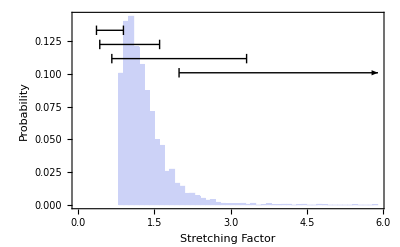

```mathematica
κHistogramPlot[sample4096⟦All,-1⟧,κObserved]
```

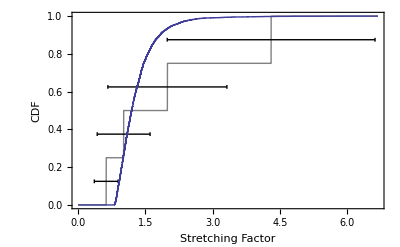

```mathematica
κCDFPlot[sample4096⟦All,-1⟧,κObserved,PlotPoints->4096]
```

#### Correlation plots

```mathematica
highFractionκObserved={
{0.0604813{1-1/√17,1+1/√17},{0.665059,3.31859}},
{0.124288{1-1/√26,1+1/√26},{0.42816,1.60589}},
{0.141906{1-1/√51.1454,1+1/√51.1454},{0.363328,0.893781}},
{0.0572066{1-1/√27,1+1/√27},{1.98748,6.62006}}
};
```

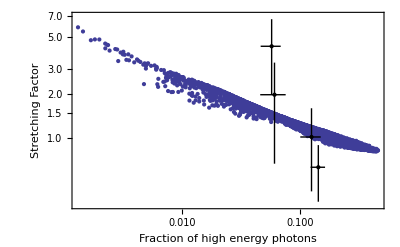

```mathematica
ratioκListPlot[sample4096⟦All,{3,4,-1}⟧,highFractionκObserved,PlotRange->{All,{0.95Min[Min@highFractionκObserved⟦All,2,1⟧,Min@sample4096⟦All,6⟧],1.05Max[Max@highFractionκObserved⟦All,2,2⟧,Max@sample4096⟦All,6⟧]}}]
```

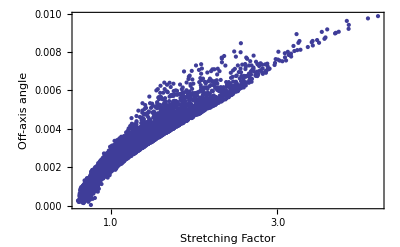

```mathematica
χκListPlot[sample4096⟦All,{2,-1}⟧]
```

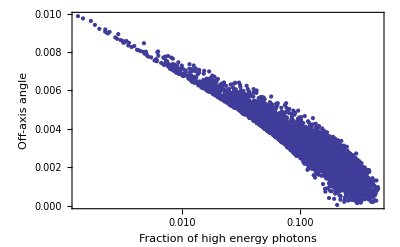

```mathematica
ratioχListPlot[sample4096⟦All,{2,3,4}⟧,PlotRange->All]
```

#### Burst CDF plots

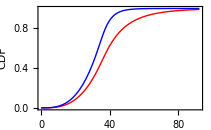

```mathematica
PrintTemporary[Dynamic[τ]];
burstCDFPlot[defaultUniverse[],defaultBurst[],defaultObserver[z->1.822,χ->0],{.1,1.,∞},{1.,1.}]
```

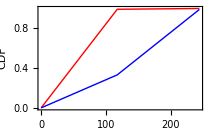

```mathematica
PrintTemporary[Dynamic[τ]];
burstCDFPlot[defaultUniverse[],defaultBurst[],defaultObserver[],{.1,1.,∞},{1.,1.},PlotPoints->3,MaxRecursion->0,ImageSize->.45itepLineWidth,FontSize->12]
```

#### Very High Energy Bursts Fraction

```mathematica
PrintTemporary[Dynamic[z]];
burstFraction[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞}]
```

0.115619

## Extra

### Plots for papers and posters

#### Common procedures

### Plots for papers and posters

#### Main paper

```mathematica
lineWidth=469.75502;
fontSize=10;
```

```mathematica
Export["Paper/modelOverview.pdf",modelScheme[centralEngineSize->.03,jetRadius->.5,lowAngle->.43,highAngle->.043,observerSize->.03,observerDistance->1.,observerAngle->.4,centralEngineLabelQ->True,jetLabelQ->True,observerLabelQ->True,FontSize->fontSize,ImageSize->.7lineWidth]];
```

```mathematica
PrintTemporary[Dynamic[τ]];
Export["Paper/sampleLightCurveLogNegative.pdf",burstCDFPlot[defaultUniverse[],defaultBurst[],defaultObserver[z->1.822,χ->0.],{.1,1.,∞},{1.,1.},ImageSize->.45lineWidth,FontSize->fontSize]];
Export["Paper/sampleLightCurveLogPositive.pdf",burstCDFPlot[defaultUniverse[],defaultBurst[],defaultObserver[],{.1,1.,∞},{1.,1.},ImageSize->.45lineWidth,FontSize->fontSize]];
```

$Aborted

$Aborted

```mathematica
dir080916C="GRObservations/DerivedData/GRObservations/Build/Products/Release/080916C/";
dir090510="GRObservations/DerivedData/GRObservations/Build/Products/Release/090510/";
dir090902B="GRObservations/DerivedData/GRObservations/Build/Products/Release/090902B/";
dir090926A="GRObservations/DerivedData/GRObservations/Build/Products/Release/090926A/";
bursts={dir080916C,dir090510,dir090902B,dir090926A};
ranges={
{-0.05 300,300},
{-0.05 60,60},
{-0.05 1000,1000},
{-0.05 300,300}
};
gevData=Table[Import[burst<>"gev","Table"],{burst,bursts}];
mevData=Table[Import[burst<>"mev","Table"],{burst,bursts}];
probData=Table[Import[burst<>"probs","Table"]/.{κ_,p_,a_,b_,c_}->{κ,p},{burst,bursts}];
Do[Export["Paper/lightCurve"<>ToString[FileNameSplit[bursts⟦i⟧]⟦-1⟧]<>".pdf",ListLinePlot[{mevData[[i]],gevData[[i]]},PlotRange->{ranges[[i]],All},PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photon Fraction"},PlotLegends->Placed[{Style["0.1 – 1 GeV",FontSize->fontSize],Style["1 – 300 GeV",FontSize->fontSize]},{0.74,0.20}],ImageSize->.45lineWidth,FrameStyle->Directive[FontSize->fontSize]]],{i,1,Length[mevData]}];
Do[Export["Paper/probabilities"<>ToString[FileNameSplit[bursts⟦i⟧]⟦-1⟧]<>".pdf",
ListLogPlot[probData[[i]],Joined->True,PlotRange->{{0,10},{1.*^-12,1.}},PlotStyle->RGBColor[0.5,0,0.5],Frame->{{True,False},{True,False}},FrameLabel->{"Stretching Factor","KS Probability"},ImageSize->.45lineWidth,FrameStyle->Directive[FontSize->fontSize]]],{i,1,Length[mevData]}];
```

```mathematica
κObserved={
{"090902B",{0.363408,0.893437}},
{"090510",{0.428137,1.60485}},
{"080916C",{0.66529,3.31569}},
{"090926A",{1.98759,6.61486}}
};
Export["Paper/kappaDistributionHistogram.pdf",κHistogramPlot[sample4096⟦All,-1⟧,κObserved,FontSize->fontSize,ImageSize->.45lineWidth]];
Export["Paper/kappaDistributionCDF.pdf",κCDFPlot[sample4096⟦All,-1⟧,κObserved,PlotPoints->4096,FontSize->fontSize,ImageSize->.45lineWidth]];
```

```mathematica
highFractionκObserved={
{0.0643747{1-1/√17,1+1/√17},{0.665059,3.31859}},
{0.141928{1-1/√26,1+1/√26},{0.42816,1.60589}},
{0.165373{1-1/√51.1454,1+1/√51.1454},{0.363328,0.893781}},
{0.0606777{1-1/√27,1+1/√27},{1.98748,6.62006}}
};
Export["Paper/correlations.pdf",GraphicsGrid[{
{ratioχListPlot[sample4096⟦All,{2,3,4}⟧,{},ImagePadding->{{50,5},{30,5}},FontSize->fontSize,ImageSize->.45lineWidth,FrameTicks->{{0.01,0.1}~Join~Flatten[Table[Table[{it,""},{it,10^sc,10^(sc+1),10^sc}],{sc,-3,-1}],1],Automatic},PointSize->Tiny],
χκListPlot[sample4096⟦All,{2,-1}⟧,{},ImagePadding->{{50,5},{30,5}},PlotRange->All,FontSize->fontSize,ImageSize->.45lineWidth,PointSize->Tiny]},

{ratioκListPlot[sample4096⟦All,{3,4,-1}⟧,highFractionκObserved,ImagePadding->{{50,5},{30,5}},PlotRange->{All,{0.42,6.7}},FontSize->10,ImageSize->.45lineWidth,FrameTicks->{{0.01,0.1}~Join~Flatten[Table[Table[{it,""},{it,10^sc,10^(sc+1),10^sc}],{sc,-3,-1}],1],Automatic},PointSize->Tiny],
Graphics[]}
}]];
```

#### ITEP Proceedings

```mathematica
itepLineWidth=469.47046;
itepFontSize=10;
```

```mathematica
dir090902B="GRObservations/DerivedData/GRObservations/Build/Products/Release/090902B/";
dir090926A="GRObservations/DerivedData/GRObservations/Build/Products/Release/090926A/";
bursts={dir090902B,dir090926A};
ranges={
{-0.05 1000,1000},
{-0.05 300,300}
};
gevData=Table[Import[burst<>"gev","Table"],{burst,bursts}];
mevData=Table[Import[burst<>"mev","Table"],{burst,bursts}];
probData=Table[Import[burst<>"probs","Table"]/.{κ_,p_,a_,b_,c_}->{κ,p},{burst,bursts}];
Do[Export["ITEPProceedings/p"<>ToString[i]<>".pdf",GraphicsGrid[{{
ListLinePlot[{mevData[[i]],gevData[[i]]},PlotRange->{ranges[[i]],All},PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photon Fraction"},PlotLegends->Placed[{Style["0.1 – 1 GeV",FontSize->itepFontSize],Style["1 – 300 GeV",FontSize->itepFontSize]},{0.74,0.20}],ImageSize->.45itepLineWidth,FrameStyle->Directive[FontSize->itepFontSize]],
ListLogPlot[probData[[i]],Joined->True,PlotRange->{{0,10},{1.*^-12,1.}},PlotStyle->RGBColor[0.5,0,0.5],Frame->{{True,False},{True,False}},FrameLabel->{"Stretching Factor","KS Probability"},ImageSize->.45itepLineWidth,FrameStyle->Directive[FontSize->itepFontSize]]
}},ImageSize->itepLineWidth]],{i,1,Length[mevData]}];
```

```mathematica
Export["ITEPProceedings/p3.pdf",modelScheme[centralEngineSize->.03,jetRadius->.5,lowAngle->.43,highAngle->.043,observerSize->.03,observerDistance->1.,observerAngle->.4,centralEngineLabelQ->True,jetLabelQ->True,observerLabelQ->True,FontSize->itepFontSize,ImageSize->.7itepLineWidth]];
```

```mathematica
PrintTemporary[Dynamic[τ]];
Export["ITEPProceedings/p4.pdf",GraphicsGrid[{{
burstCDFPlot[defaultUniverse[],defaultBurst[],defaultObserver[z->1.822,χ->0.],{.1,1.,∞},{1.,1.},ImageSize->.45itepLineWidth,FontSize->itepFontSize],
burstCDFPlot[defaultUniverse[],defaultBurst[],defaultObserver[],{.1,1.,∞},{1.,1.},ImageSize->.45itepLineWidth,FontSize->itepFontSize]
}},ImageSize->itepLineWidth]];
```

```mathematica
κObserved={
{"090902B",{0.363408,0.893437}},
{"090510",{0.428137,1.60485}},
{"080916C",{0.66529,3.31569}},
{"090926A",{1.98759,6.61486}}
};
Export["ITEPProceedings/p5.pdf",GraphicsGrid[{{
κHistogramPlot[sample4096⟦All,-1⟧,κObserved,FontSize->itepFontSize,ImageSize->.45itepLineWidth],
κCDFPlot[sample4096⟦All,-1⟧,κObserved,PlotPoints->4096,FontSize->itepFontSize,ImageSize->.45itepLineWidth]
}},ImageSize->itepLineWidth]];
```

```mathematica
highFractionκObserved={
{0.0604813{1-1/√17,1+1/√17},{0.665059,3.31859}},
{0.124288{1-1/√26,1+1/√26},{0.42816,1.60589}},
{0.141906{1-1/√51.1454,1+1/√51.1454},{0.363328,0.893781}},
{0.0572066{1-1/√27,1+1/√27},{1.98748,6.62006}}
};
Export["ITEPProceedings/p6.pdf",GraphicsGrid[{{
ratioκListPlot[sample4096⟦All,{3,4,-1}⟧,highFractionκObserved,PlotRange->{All,{0.42,6.7}},FontSize->itepFontSize,ImageSize->.45itepLineWidth,FrameTicks->{{0.01,0.1}~Join~Flatten[Table[Table[{it,""},{it,10^sc,10^(sc+1),10^sc}],{sc,-3,-1}],1],Automatic}],

ratioχListPlot[sample4096⟦All,{2,3,4}⟧,FontSize->itepFontSize,ImageSize->.45itepLineWidth,FrameTicks->{{0.01,0.1}~Join~Flatten[Table[Table[{it,""},{it,10^sc,10^(sc+1),10^sc}],{sc,-3,-1}],1],Automatic}]
}}]];
```